```mathematica
data=Select[Import["/home/nils/uni/Papers/2017/input-transformations/experiments/aggregated","TSV"],Length[#]>=11&];
```

```mathematica
Length[data]
```

6613

```mathematica
data=Select[
data,
#[[4]]==64  (* n *)
&&#[[5]]≥1 (* k *)
&
];
```

```mathematica
groupedData=GroupBy[data,{#[[4]],#[[5]],#[[7]],#[[8]]}&];
```

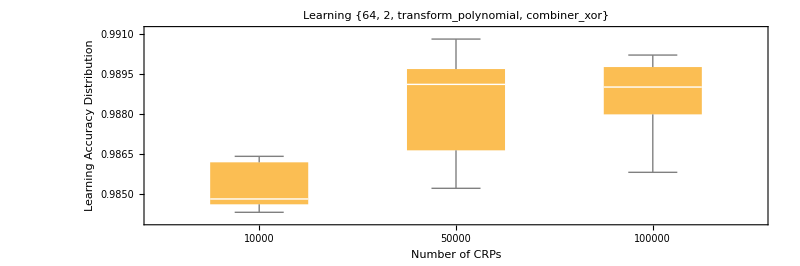
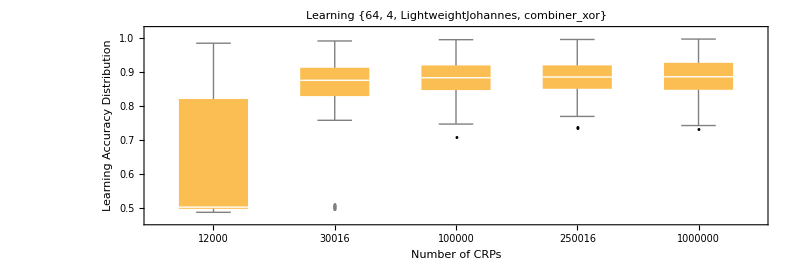
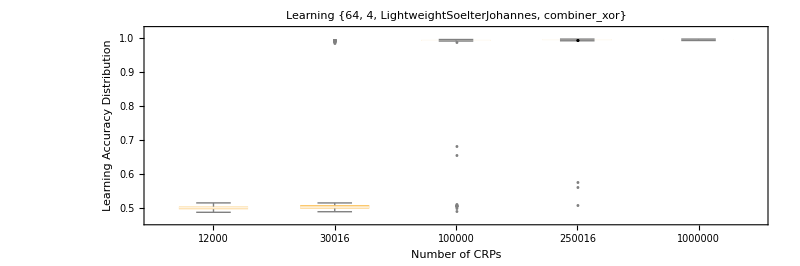
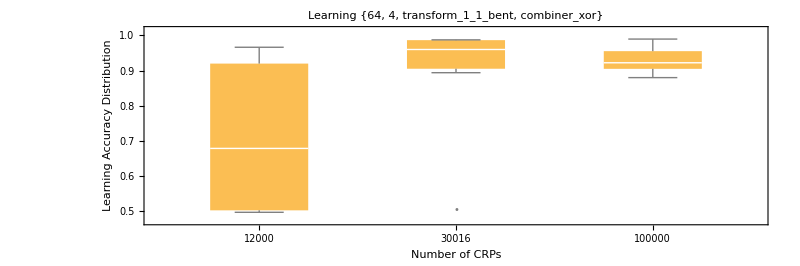
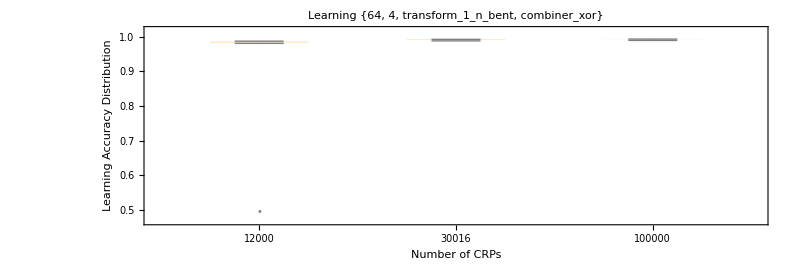
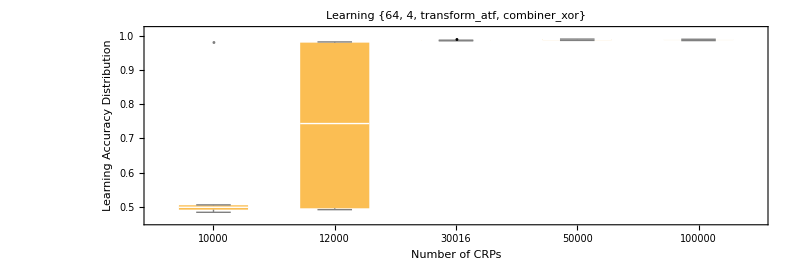
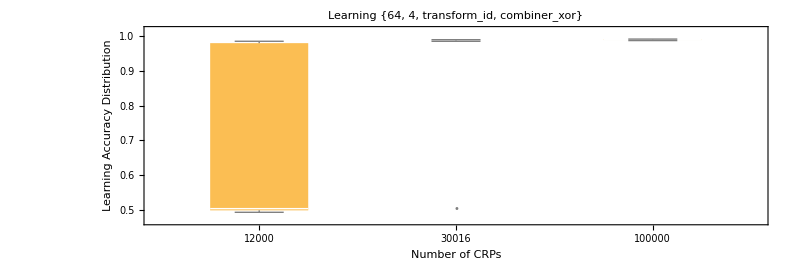
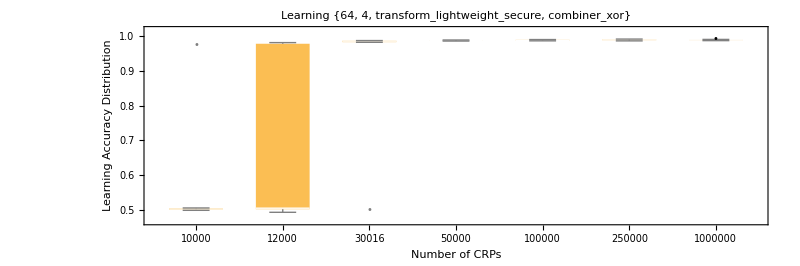

```mathematica
Table[
Module[{aggregatedData},
aggregatedData=KeySort[SortBy[GroupBy[groupedData[group],#[[6]]&,#[[All,11]]&],First]];
BoxWhiskerChart[
Values[
aggregatedData
],
"Outliers",
ChartLabels->Keys[aggregatedData],
ImageSize->800,
PlotRangePadding->0,
PlotLabel->"Learning " <> ToString[group],
AspectRatio->1/3,
FrameLabel->{"Number of CRPs","Learning Accuracy Distribution"}
]
],
{group,SortBy[Keys[groupedData],#[[1]]&]}
]
```

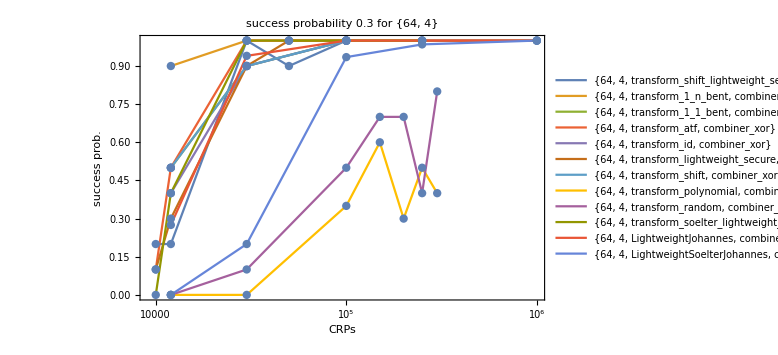
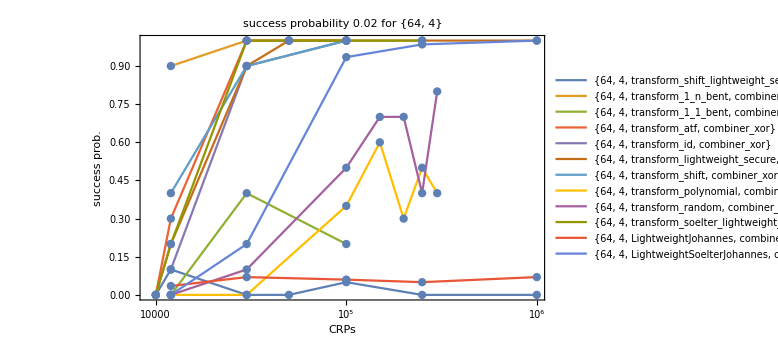
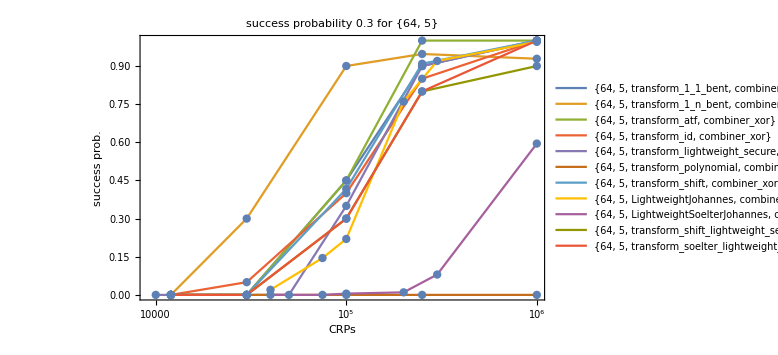
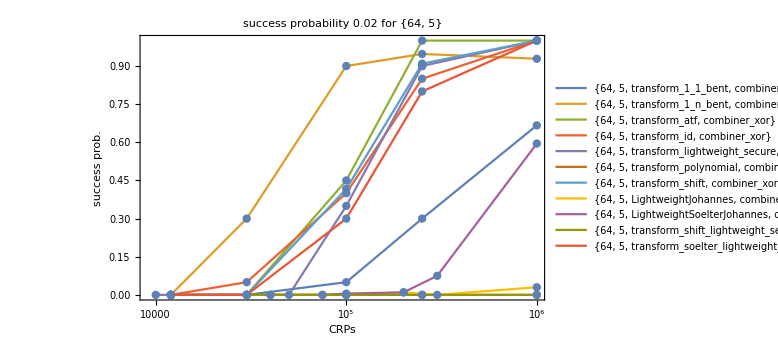
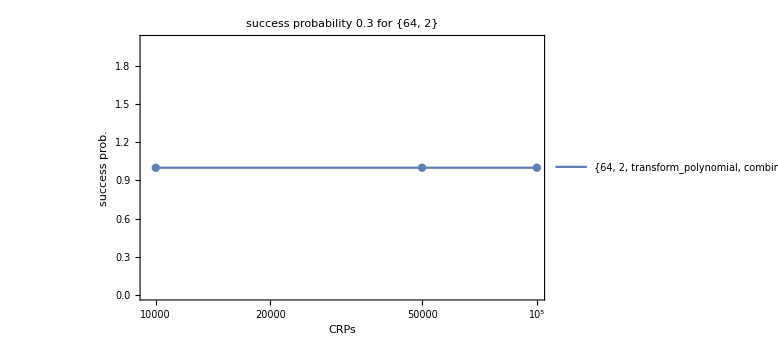
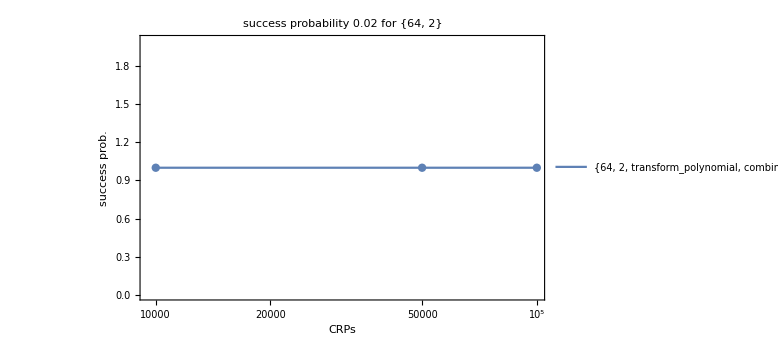

```mathematica
Module[{groups,filteredKeys},
groups=GroupBy[Keys[groupedData],{#[[1]],#[[2]]}&];
Table[
filteredKeys=groups[group];
Table[
ListLogLinearPlot[
Table[
Module[{aggregatedData},
aggregatedData=GroupBy[
groupedData[group],
#[[6]]&,
Length[Select[#[[All,11]],#>1-c&]]/Length[#[[All,11]]]&
];
SortBy[Transpose[{Keys[aggregatedData],Values[aggregatedData]}],#[[1]]&]
],
{group,filteredKeys}
],
Mesh->Full,
ImageSize->Large,
PlotLabel->"success probability "<>ToString[c] <> " for " <> ToString[group],
FrameLabel->{"CRPs","success prob."},
Frame->True,
PlotLegends->ToString/@filteredKeys,
Joined->True,
PlotRange->Full
],
{c,{0.3,0.02}}
],
{group,Keys[groups]}
]
]
```